```mathematica
u090494e　荒井直幸　2014年12月9日
```

```mathematica
課題１
```

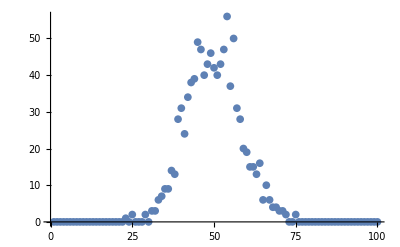

ReplaceAll::reps: は置換則リストあるいは有効なディスパッチテーブルではないため，置換に使用できません．

General::ivar: 44は有効な変数ではありません．

FindFit[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,2,0,3,3,6,7,9,9,14,13,28,31,24,34,38,39,49,47,40,43,46,42,40,43,47,56,37,50,31,28,20,19,15,15,13,16,6,10,6,4,4,3,3,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{a ⅇ^(-1936 b),a ⅇ^(-b (-6+c)^2)/.-Graphics-},{a,b,c},44]

```mathematica
list1=Table[0,{100}];
i=0;
While[i<1000,
x=50;
j=0;
While[j<100,
x+=RandomInteger[{-1,1}];
j++];
list1[[x]]++
i++]
graph1=ListPlot[list1]
FindFit[list1,{a*Exp[-b*x^2],a*Exp[-b*(x-50+c)^2]/.%},{a,b,c},x]
```

```mathematica
課題２
```

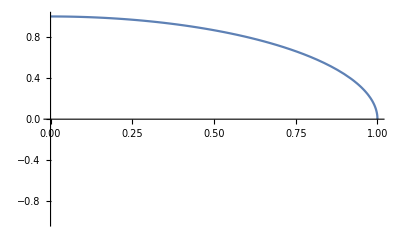

1.5708

```mathematica
func1[k_]:=√(1^2-k^2);
Plot[func1[x],{x,0,1},PlotRange->{-1,1}]
NIntegrate[func1[x],{x,-1,1}]
```

```mathematica
func1[k_]:=√(1^2-k^2);
i=0;
j=0;
While[i<1000000,
x=RandomReal[{0,1}];
y=RandomReal[{0,1}];
If[y<func1[x],j++];
If[y==func1[x],j=j+1/2];
i++]
N[4 j/i]
```

3.1435

```mathematica
課題３
```

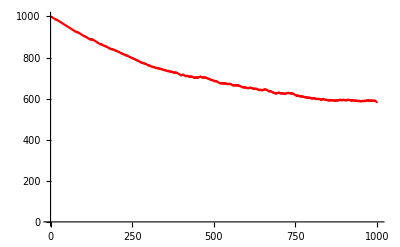

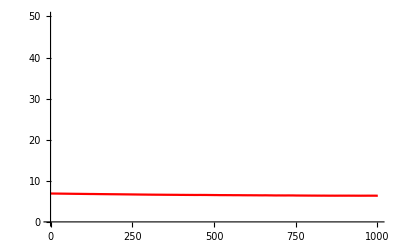

```mathematica
i=0;
hidari=1000;migi=0;
list2={};list3={};list4={};
AppendTo[list2,hidari];
AppendTo[list3,migi];
While[i<1000,wariai=hidari/1000;
If[wariai>RandomReal[{0,1}],
{hidari--;migi++},
{hidari++;migi--}];
AppendTo[list2,hidari];
AppendTo[list3,migi];
AppendTo[list4,hidari+migi];i++]
graph2=ListPlot[list2,Joined->True,PlotRange->{0,1000},PlotStyle->RGBColor[{1,0,0}]];
graph3=ListPlot[list3,Joined->True,PlotRange->{0,1000}];
graph4=ListPlot[list4,Joined->True,PlotRange->{0,1000},PlotStyle->RGBColor[{0,1,0}]];
Show[graph2]
graph5=ListPlot[Log[list2],Joined->True,PlotRange->{{0,1000},{0,50}},PlotStyle->RGBColor[{1,0,0}]];
Show[graph5]
```